```mathematica
Remove["Global`*"];
(* Here is the complete program. Just put in your RealData, z position, and approximate spot size radius at that location. *)
(* See the above tutorial for an explanation of logic.*)
z5=Import["/Users/seth/Desktop/LaserParameters/thursday5inches.csv"];
z10=Import["/Users/seth/Desktop/LaserParameters/thursday10inches.csv"];
z15=Import["/Users/seth/Desktop/LaserParameters/thursday15inches.csv"];
z20=Import["/Users/seth/Desktop/LaserParameters/thrusday20inches.csv"];
z33=Import["/Users/seth/Desktop/LaserParameters/thursday33inches.csv"];
z38=Import["/Users/seth/Desktop/LaserParameters/thursday38inches.csv"];
z43=Import["/Users/seth/Desktop/LaserParameters/thursday43inches.csv"];
z48=Import["/Users/seth/Desktop/LaserParameters/thursday48inches.csv"];
z5=z5/.{x_,mV_}->{.155x,mV};
z10=z10/.{x_,mV_}->{.155x,mV};
z15=z15/.{x_,mV_}->{.155x,mV};
z20=z20/.{x_,mV_}->{.155x,mV};
z33=z33/.{x_,mV_}->{.155x,mV};
z38=z38/.{x_,mV_}->{.155x,mV};
z43=z43/.{x_,mV_}->{.155x,mV};
z48=z48/.{x_,mV_}->{.155x,mV};
```

Remove::rmnsm: There are no symbols matching "Global`*".

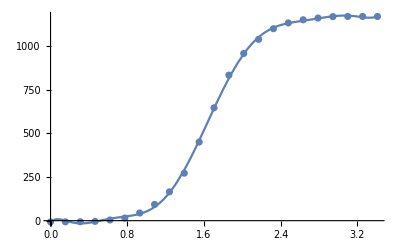

{-0.112521-0.26745 ⅈ,-0.112521+0.26745 ⅈ,0.598097-0.675874 ⅈ,0.598097+0.675874 ⅈ,1.70808,2.70648-0.758167 ⅈ,2.70648+0.758167 ⅈ,3.57154-0.358009 ⅈ,3.57154+0.358009 ⅈ,5.05627}

{1.70808}

{1.10742}

The possible beam waist at 5 inches from the laser is a member of the set {0.600655} mm

```mathematica
RealData=z5;
(* Position of measurement along axis *)
zpos=5;
(* Measured radius of visible spot size (with a ruler or the like)*)
SpotSize=3;
(* This is the precision of the measurement of the spot size. We must also assume that the razor starts to measure the beam at the same location as the ruler starts to measure the spot. Please incorporate that into your error. I find a value of 1 to be safe. *)
ErrorOfSpot=1;
MedianValueOfData=Median[RealData[[All,2]]];

(* The rest is automatic! *)
(* Fit a curve to the data *)
RealCurveFit[x_]=Fit[RealData,Table[x^n,{n,0,10}],x];
Show[
{ListPlot[RealData],
Plot[RealCurveFit[x],{x,RealData[[1]][[1]],RealData[[-1]][[1]]}]
}
]
RealMaxLocationPossibles[x_]=x/.Solve[RealCurveFit[x]==MedianValueOfData,x]
RealMaxLocationPossiblesImaginaryRemove=Select[RealMaxLocationPossibles[x],FreeQ[#, Complex]&];
RealMaxLocationPossiblesNegativeRemove=Select[RealMaxLocationPossiblesImaginaryRemove,#>0&];
RealMaxLocationSelected=Select[RealMaxLocationPossiblesNegativeRemove,#<SpotSize&]

(* Find the value of the max of the Gaussian profile *)
RealMaxValue=RealCurveFit[RealMaxLocationSelected];
(* Find the value at the location of the beam waist by definition *)
(*The definition of the radius of a laser beam with a flat-top profile is trivial,but most light beams have other transverse shapes. A frequently obtained shape is the Gaussian one,where the transverse intensity variation is described with the following equation:I(r,z) for Gaussian beam

where the beam radius w is the distance from the beam axis where the optical intensity drops to 1/e2 (≈13.5%) of the value on the beam axis.At this radius,the electric field strength drops to 1/e (≈37%) of the maximum value. (rp-photonics.com)*)
RealValueAtRadius=RealMaxValue/ⅇ^2;
(* Establish a set of possible beam waist locations *)
RealPossibleWaistLocations=x/.Solve[RealCurveFit[x]==RealValueAtRadius,x];
(* Remove the complex numbers as not possible solutions *)
PossibleWaistImaginaryRemoval=Select[RealPossibleWaistLocations,FreeQ[#, Complex]&];
(* The answer can not be larger than the location of the center of the beam *)
RealWaistLocationSelectedUpperLimit=Select[PossibleWaistImaginaryRemoval,#<(SpotSize+ErrorOfSpot)&];
(* The answer can not be negative *)
RealWaistLocationzSelected=Select[RealWaistLocationSelectedUpperLimit,#>0&]
RealBeamWaist=RealMaxLocationSelected-RealWaistLocationzSelected;
Print["The possible beam waist at ", zpos," inches from the laser is a member of the set ", RealBeamWaist, " mm"]
```

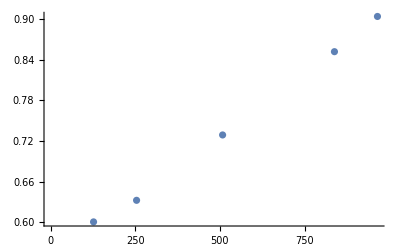

```mathematica
(* Need to check 15, 43 and 48 inches again *)
allzdata={{5,.600655},{10,.632534},(*{15,.99773},*){20,.729086},{33,.852107},{38,.904124}(*,{43,1.23857},{48,1.26888}*)};
allzdata=allzdata/.{z_,w_}->{25.4*z,w};
ListPlot[allzdata]
```